## Kittipong Tapyou 65070501003

# Homework 01 : Img2Gray, Gray2Bin

## Load Image

```mathematica
img = -Graphics-;
```

## Convert image to grayscale

```mathematica
ImgToGray[img_, weight_] := Module[{dim, grayData, imgData},
    dim = ImageDimensions[img];
    imgData = ImageData[img, "Real"];
    grayData = Table[
             weight[[1]]imgData[[i, j, 1]] + weight[[2]]imgData[[i, j, 2]] + weight[[3]]imgData[[i, j, 3]],
             {i, dim[[2]]}, {j, dim[[1]]}];
    Return[grayData];
]
```

```mathematica
grayImg = ImgToGray[img, {0.3, 0.59, 0.11}];
Image[grayImg]
```

-Graphics-

## Plot histogram of gray intensity

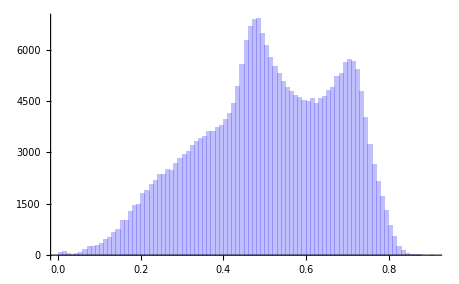

```mathematica
Histogram[Flatten[grayImg, 1], {0.01}, ChartStyle -> {Opacity[.25, Blue]}]
```

## Convert grayscale image to binary image

```mathematica
GrayToBin[img_, thres_] := Module[{dim},
	dim = Dimensions[img];
	Return[
		Table[If[img[[i, j]] > thres, 1, 0], {i, dim[[1]]}, {j, dim[[2]]}]
	];
]
```

```mathematica
Image[GrayToBin[grayImg, 0.6]]
```

-Graphics-